Bivariate normal pdf

```mathematica
M=4;
p=1/10;
d=9/10;
```

```mathematica
fXY[x_,y_,σ_]:=1/(2*Pi*σ^2)*Exp[-(x^2+y^2)/2/σ^2];
fXY[x_,y_]:=fXY[y,x,σ];
fXY[x,y]
```

(ⅇ^((-x^2-y^2)/σ^2))/(2 π σ^2)

```mathematica
Plot3D[f[x,y,1.0],{x,-3,3},{y,-3,3},PlotRange->All]
```

-Graphics3D-

and the distribution of the translated normal

```mathematica
fZ[x_,y_,ρ_,σ_]:=ρ^2*fXY[ρ*(x-1),ρ*y,σ];
fZ[x_,y_,κ_]:=fZ[x,y,κ,1];
fZ[x_,y_]:=fZ[x,y,ρ,σ];
FullSimplify[fZ[x,y]]
```

(ⅇ^(-(((-1+x)^2+y^2) ρ^2)/σ^2) ρ^2)/(2 π σ^2)

```mathematica
Plot3D[fZ[x,y,2.0,1.0],{x,-2,2},{y,-2,2},PlotRange->All]
```

-Graphics3D-

The g function

```mathematica
gt[a_]:=Integrate[x*fZ[x,x*a],{x,0,∞}]
g[ϕ_,κ_]:=Integrate[x*fZ[x,x*Tan[ϕ],κ],{x,0,∞}]
g[ϕ_]:=gt[Tan[ϕ]];
```

```mathematica
FullSimplify[g[ϕ],Element[ρ,Reals]&&Element[σ,Reals]&&Element[ϕ,Reals]&&ρ>0&&σ>0]
```

ConditionalExpression[(ⅇ^(-ρ^2/σ^2) Cos[ϕ]^2 (σ+ⅇ^((ρ^2 Cos[ϕ]^2)/σ^2) √π ρ Cos[ϕ] (Erf[(ρ Cos[ϕ])/σ]+Cos[ϕ] √(Sec[ϕ]^2))))/(4 π σ),Re[Sec[ϕ]^2]>0]

```mathematica
gtes1[ϕ_]:=Cos[ϕ]^2/4/Sqrt[Pi]*(Exp[-1]/Sqrt[Pi]+(1 +Erf[Cos[ϕ]])*Exp[-Sin[ϕ]^2]*Cos[ϕ])
```

```mathematica
gtest[ϕ_]:=NIntegrate[r/2/Pi/Sqrt[r*r-2*r*Cos[ϕ]+1]*Exp[-Sqrt[r*r-2*r*Cos[ϕ]+1]/2],{r,0,∞}]
Plot[{g[ϕ],gtest[ϕ]},{ϕ,-Pi,Pi},PlotRange->All]
```

$Aborted

```mathematica
Integrate[κ^2*r*Exp[-κ^2*(r^2 - 2*r*a+1)/2],{r,0,∞},Assumptions->{Element[κ,Reals]&&κ>0&&Element[a,Reals]}]
```

1/2 ⅇ^(-κ^2/2) (2+a ⅇ^((a^2 κ^2)/2) √(2 π) κ (1+Erf[(a κ)/(√2)]))

```mathematica
Integrate[κ^2*r^2*Exp[-κ^2*(r^2-2*r*a+1)/2],{r,0,∞},Assumptions->{Element[κ,Reals]&&κ>0&&Element[a,Reals]}]
```

(ⅇ^(-κ^2/2) (2 a κ+ⅇ^((a^2 κ^2)/2) √(2 π) (1+a^2 κ^2) (1+Erf[(a κ)/(√2)])))/(2 κ)

```mathematica
Integrate[κ^2*r^3*Exp[-κ^2*(r^2 - 2*r*a+1)/2],{r,0,∞},Assumptions->{Element[κ,Reals]&&κ>0&&Element[a,Reals]}]
```

(ⅇ^(-κ^2/2) (4+2 a^2 κ^2+a ⅇ^((a^2 κ^2)/2) √(2 π) κ (3+a^2 κ^2) (1+Erf[(a κ)/(√2)])))/(2 κ^2)

```mathematica
Integrate[κ*r^2*Cos[ϕ]*Exp[-κ^2*(r^2 - 2*r*Cos[ϕ]+1)/2],{ϕ,-π/2,π/2},Assumptions->{Element[κ,Reals]&&κ>0}]
```

ⅇ^(-1/2 (1+r^2) κ^2) π r^2 κ (BesselI[1,r κ^2]+StruveL[-1,r κ^2])

```mathematica
2 ⅇ^(-1/2 (1+r^2) κ^2) π r^2 κ BesselI[1,r κ^2]
```

```mathematica
Integrate[2 ⅇ^(-1/2 (1+r^2) κ^2) π r^2 κ BesselI[1,r κ^2],{r,0,∞},Assumptions->{Element[κ,Reals]&&κ>0}]
```

(2 π)/κ

```mathematica
Series[x*Exp[I*x],{x,0,1}]
```

x+O[x]^2

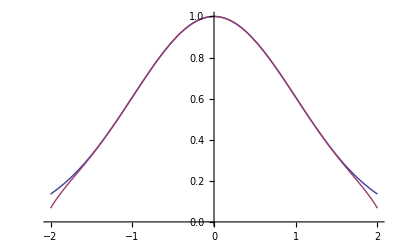

```mathematica
Plot[{Exp[-x^2/2],Sum[(-1)^n*x^(2*n)/2^n/Factorial[n],{n,0,5}]},{x,-2,2}]
```

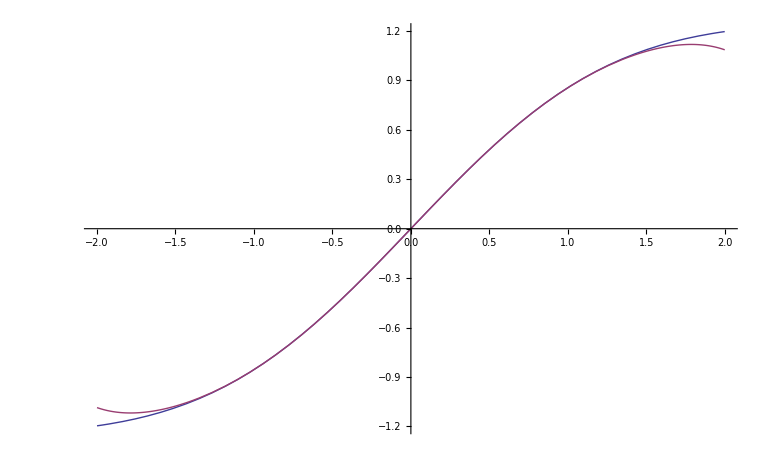

```mathematica
Plot[{Sqrt[Pi]/Sqrt[2]*Erf[x/Sqrt[2]],Sum[(-1)^n*x^(2*n+1)/(2*n+1)/2^n/Factorial[n],{n,0,3}]},{x,-2,2}]
```

```mathematica
phi = 0.4*Pi;
psi[t_]:=Integrate[Exp[-x^2/2],{x,-Infinity,t}]/Sqrt[2*Pi]
```

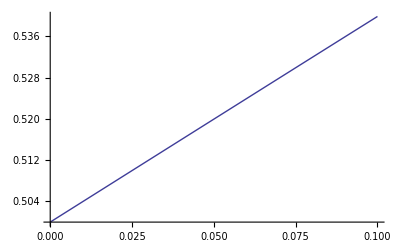

```mathematica
Plot[psi[t],{t,1/10000,1/10}]
```

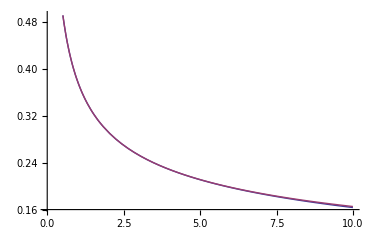

```mathematica
Plot[{psi[Sqrt[2*k]*Cos[phi]]/Sqrt[Pi*k],1/2/Sqrt[Pi*k]+Sum[(-1)^n*Cos[phi]^(2*n+1)*k^n/Factorial[n]/(2*n+1)/Pi,{n,0,2}]},{k,1/1000,10}]
```

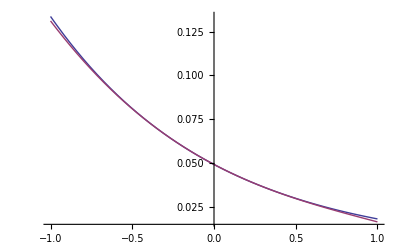

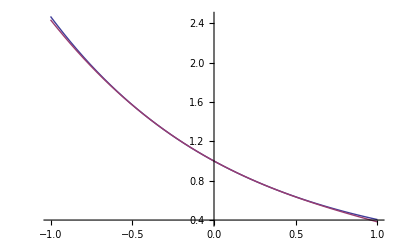

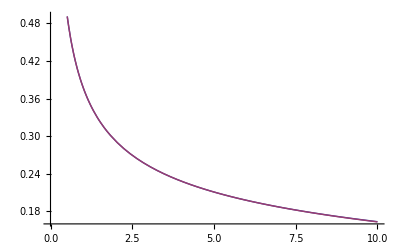

```mathematica
testfunc[k_]:=psi[Sqrt[2*k]*Cos[phi]]/Sqrt[Pi*k]*Exp[-k*Sin[phi]^2];
a[n_]:=(-1)^n*Cos[phi]/2/Pi/Factorial[n];
Plot[{Cos[phi]/2/Pi*Exp[-k],Sum[a[n]*k^n,{n,0,3}]},{k,-1,1}]
b[n_]:=(-1)^n*Sin[phi]^(2*n)/Factorial[n];
Plot[{Exp[-k*Sin[phi]^2],Sum[b[n]*k^n,{n,0,3}]},{k,-1,1}]
c[n_]:=(-1)^n*Cos[phi]^(2*n+1)/Factorial[n]/(2*n+1)/Pi;
Plot[{psi[Sqrt[2*k]*Cos[phi]]/Sqrt[Pi*k],1/2/Sqrt[Pi*k] + Sum[c[n]*k^n,{n,0,3}]},{k,1/1000,10}]
```

```mathematica
d[n_]:=Sum[b[n-s]*c[s],{s,0,n}]
```

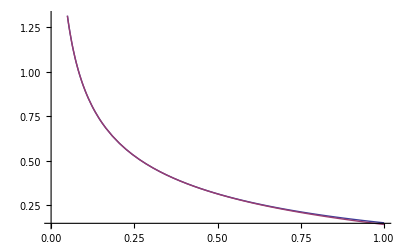

```mathematica
Plot[{testfunc[k],1/2/Sqrt[Pi*k]*Sum[b[n]*k^n,{n,0,3}]+Sum[d[n]*k^n,{n,0,3}]},{k,1/1000,1}]
```

```mathematica
g[k_]:=Cos[phi]/2/Pi*Exp[-k]+testfunc[k]*(2+Cos[phi]^2*k);
b[-1]:=0;
d[-1]:=0;
ell[n_]:=1/2/Sqrt[Pi]*(2*b[n]+Cos[phi]^2*b[n-1])
q[n_]:=a[n]+2*d[n]+Cos[phi]^2*d[n-1]
```

```mathematica
g1[k_]:=Sum[ell[n]*k^n,{n,0,5}]/Sqrt[k] + Sum[q[n]*k^n,{n,0,5}]
```

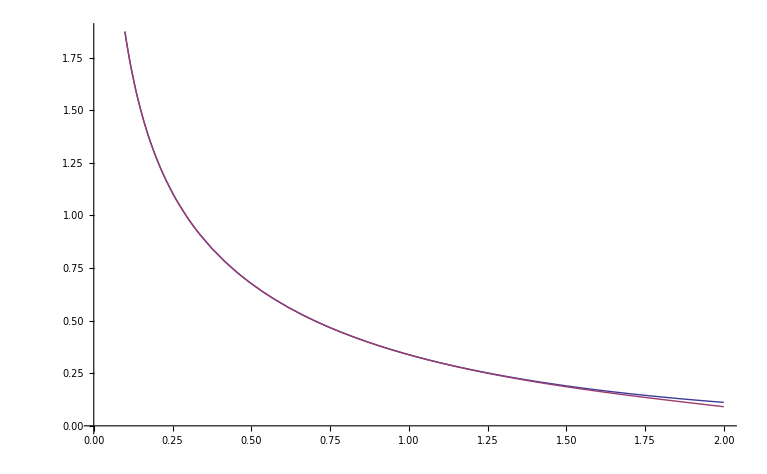

```mathematica
Plot[{g[k],g1[k]},{k,1/100,2}]
```

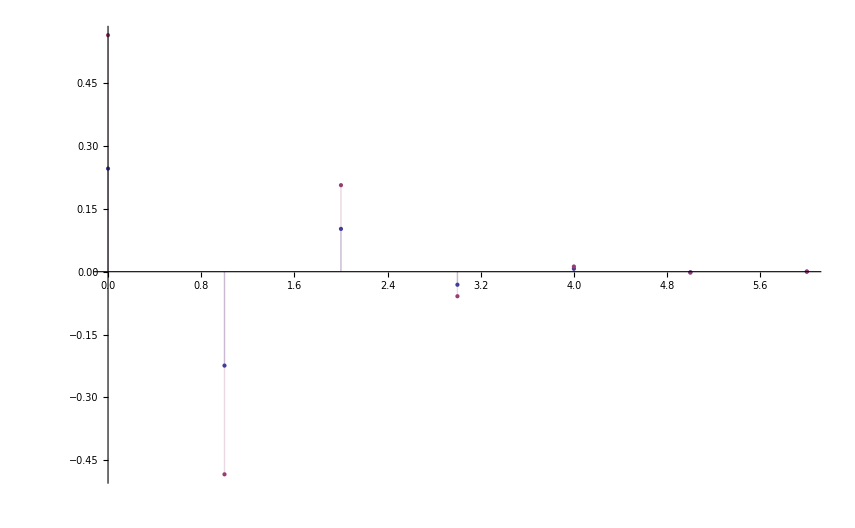

```mathematica
DiscretePlot[{q[n],ell[n]},{n,0,6}]
```